```mathematica
sig[x_]:=1/(1+E^(-x))
```

```mathematica
nn[x_,θ_,f_:Tanh]:=Module[{w11,w12,w13,w14,w21,w22,w23},
{w11,w12,w13,w14,w21,w22,w23} = θ;
Return[f[w21*f[w11*x+w12]+w22*f[w13*x+w14]+w23]];
 Return[f[w21*f[w11*f[x]+w12]+w22*f[w13*f[x]+w14]+w23]];
Return[w21*f[w11*x+w12]+w22*f[w13*x+w14]+w23];
]
```

```mathematica
gradient[x_,weights_,fn_:Tanh]:=Module[{w11,w12,w13,w14,w21,w22,w23,w,d},
w={w11,w12,w13,w14,w21,w22,w23};
d=D[nn[x,w,fn],{w}]/.MapThread[#1->#2&,{w,weights}];
Return[d]
]
```

```mathematica
D[-1/2(y-nn[x,{w11,w12,w13,w14,w21,w22,w23},f])^2,{{w11,w12,w13,w14,w21,w22,w23}}]//TableForm
```

w21 x (y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w12+w11 x] f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]
w21 (y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w12+w11 x] f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]
w22 x (y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w14+w13 x] f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]
w22 (y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w14+w13 x] f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]
f[w12+w11 x] (y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]
f[w14+w13 x] (y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]
(y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]

```mathematica
(*
Implement a simple backpropagation algorithm and print out the
weights along the way. Use this to really understand what is 
going on. And then use it as a way to generate data to test your
software with. Eg, you can generate the entire sequience of weights,
 outputs, and errors for 10, 100, or even 1000 iterations of 
backpropagation and use that to verify your python program.
*)
```

```mathematica
train[data_,init_,lr_:.1,epochs_:100]:=Module[{θ,errors,adjust,batches},
θ=init;
Do[
errors = Map[d↦{d[[1]],d[[2]]-nn[d[[1]],θ]},data];
adjust =Table[θ +=gradient[e[[1]],θ]*e[[2]]*lr,{e,errors}];
(*,{e,RandomSample[errors,10]}]*)
(* θ += Mean@adjust *)
,{epochs}]
Return[θ];
]
```

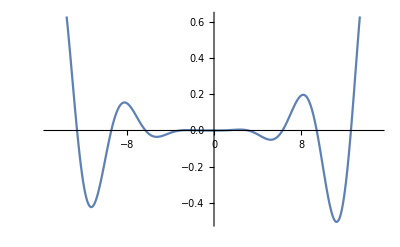

```mathematica
Plot[(x+x^2+x^3)*Sin[x]/3000,{x,-15,15}]
```

```mathematica
data={{2,.9},{1,.3},{-1,.4},{-2,.1}};
data2=Table[{x,(x+x^2+x^3)*Sin[x]/4000},{x,-15,15,.5}];
θ = {.4,-.2,.6,.1,.4,-.2,.6};
```

{0.44548,-8.1177,0.211708,3.06551,1.40588,-0.306272,1.52515}

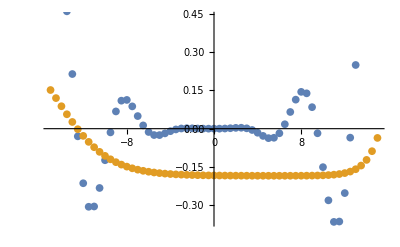

```mathematica
nθ = train[data2, θ,.01,10000]
nnData =Map[in ↦{in, nn[in,nθ]},data2[[All,1]]];
ListPlot[{data2,nnData}]
```

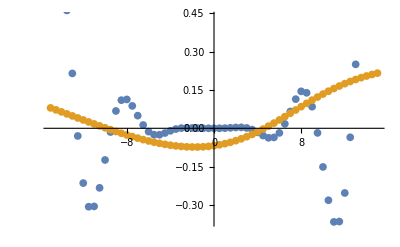

```mathematica
ListPlot[Flatten[θs,1]ᵀ]
```

-Graphics-

```mathematica
NonlinearModelFit[data,a+b*x+c*x^2+d*x^3,{a,b,c,d},x]
```

FittedModel[0.3-0.133333 x+0.05 x^2+0.0833333 x^3]

```mathematica
(* Create a general neural network structure generator. That can be
used to graph the network, produce partial derivative table, and other metadata. *)
NODES = "nodes";
ACTIVATION = "activation";
BIASED = "biased";
nnConfig={
<|NODES->1, ACTIVATION->Symbol["in"], BIASED->True|>,
<|NODES->4, ACTIVATION->Symbol["hid"], BIASED->True|>,
<|NODES->3, ACTIVATION->Symbol["hid"], BIASED->True|>,
<|NODES->2, ACTIVATION->Symbol["out"], BIASED->False|>
};
```

```mathematica
nnStruct=NetworkStructure[nnConfig]
feedForwardNN =FullyConnected[nnStruct];
weights=WeightVector[feedForwardNN];
grad=SymbolicGradient[feedForwardNN,weights];
fnGrad=grad/.{in->(x↦x),hid->Tanh,out->(x↦x)};
feedForwardNN
weights//Sort
Map[TableForm,Table[{weights[[i]],g[[i]]},{g,fnGrad},{i,1,Length[g]}]]
```

{{in[x1],1},{hid[x1],hid[x2],hid[x3],hid[x4],1},{hid[x1],hid[x2],hid[x3],1},{out[x1],out[x2]}}

{out[w3¸4+w3¸3 hid[w2¸15+w2¸11 hid[w1¸2+w1¸1 in[x1]]+w2¸12 hid[w1¸4+w1¸3 in[x1]]+w2¸13 hid[w1¸6+w1¸5 in[x1]]+w2¸14 hid[w1¸8+w1¸7 in[x1]]]+w3¸1 hid[w2¸5+w2¸1 hid[w1¸2+w1¸1 in[x1]]+w2¸2 hid[w1¸4+w1¸3 in[x1]]+w2¸3 hid[w1¸6+w1¸5 in[x1]]+w2¸4 hid[w1¸8+w1¸7 in[x1]]]+w3¸2 hid[w2¸10+w2¸6 hid[w1¸2+w1¸1 in[x1]]+w2¸7 hid[w1¸4+w1¸3 in[x1]]+w2¸8 hid[w1¸6+w1¸5 in[x1]]+w2¸9 hid[w1¸8+w1¸7 in[x1]]]],out[w3¸8+w3¸7 hid[w2¸15+w2¸11 hid[w1¸2+w1¸1 in[x1]]+w2¸12 hid[w1¸4+w1¸3 in[x1]]+w2¸13 hid[w1¸6+w1¸5 in[x1]]+w2¸14 hid[w1¸8+w1¸7 in[x1]]]+w3¸5 hid[w2¸5+w2¸1 hid[w1¸2+w1¸1 in[x1]]+w2¸2 hid[w1¸4+w1¸3 in[x1]]+w2¸3 hid[w1¸6+w1¸5 in[x1]]+w2¸4 hid[w1¸8+w1¸7 in[x1]]]+w3¸6 hid[w2¸10+w2¸6 hid[w1¸2+w1¸1 in[x1]]+w2¸7 hid[w1¸4+w1¸3 in[x1]]+w2¸8 hid[w1¸6+w1¸5 in[x1]]+w2¸9 hid[w1¸8+w1¸7 in[x1]]]]}

{w1¸1,w1¸2,w1¸3,w1¸4,w1¸5,w1¸6,w1¸7,w1¸8,w2¸1,w2¸10,w2¸11,w2¸12,w2¸13,w2¸14,w2¸15,w2¸2,w2¸3,w2¸4,w2¸5,w2¸6,w2¸7,w2¸8,w2¸9,w3¸1,w3¸2,w3¸3,w3¸4,w3¸5,w3¸6,w3¸7,w3¸8}

{w3¸4 | 1
w3¸3 | Tanh[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]
w2¸15 | w3¸3 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2
w2¸11 | w3¸3 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸2+w1¸1 x1]
w1¸2 | Sech[w1¸2+w1¸1 x1]^2 (w2¸11 w3¸3 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2+w2¸1 w3¸1 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2+w2¸6 w3¸2 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2)
w1¸1 | x1 Sech[w1¸2+w1¸1 x1]^2 (w2¸11 w3¸3 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2+w2¸1 w3¸1 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2+w2¸6 w3¸2 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2)
w2¸12 | w3¸3 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸4+w1¸3 x1]
w1¸4 | Sech[w1¸4+w1¸3 x1]^2 (w2¸12 w3¸3 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2+w2¸2 w3¸1 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2+w2¸7 w3¸2 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2)
w1¸3 | x1 Sech[w1¸4+w1¸3 x1]^2 (w2¸12 w3¸3 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2+w2¸2 w3¸1 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2+w2¸7 w3¸2 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2)
w2¸13 | w3¸3 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸6+w1¸5 x1]
w1¸6 | Sech[w1¸6+w1¸5 x1]^2 (w2¸13 w3¸3 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2+w2¸3 w3¸1 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2+w2¸8 w3¸2 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2)
w1¸5 | x1 Sech[w1¸6+w1¸5 x1]^2 (w2¸13 w3¸3 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2+w2¸3 w3¸1 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2+w2¸8 w3¸2 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2)
w2¸14 | w3¸3 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸8+w1¸7 x1]
w1¸8 | Sech[w1¸8+w1¸7 x1]^2 (w2¸14 w3¸3 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2+w2¸4 w3¸1 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2+w2¸9 w3¸2 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2)
w1¸7 | x1 Sech[w1¸8+w1¸7 x1]^2 (w2¸14 w3¸3 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2+w2¸4 w3¸1 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2+w2¸9 w3¸2 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2)
w3¸1 | Tanh[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]
w2¸5 | w3¸1 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2
w2¸1 | w3¸1 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸2+w1¸1 x1]
w2¸2 | w3¸1 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸4+w1¸3 x1]
w2¸3 | w3¸1 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸6+w1¸5 x1]
w2¸4 | w3¸1 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸8+w1¸7 x1]
w3¸2 | Tanh[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]
w2¸10 | w3¸2 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2
w2¸6 | w3¸2 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸2+w1¸1 x1]
w2¸7 | w3¸2 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸4+w1¸3 x1]
w2¸8 | w3¸2 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸6+w1¸5 x1]
w2¸9 | w3¸2 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸8+w1¸7 x1]
w3¸8 | 0
w3¸7 | 0
w3¸5 | 0
w3¸6 | 0,w3¸4 | 0
w3¸3 | 0
w2¸15 | w3¸7 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2
w2¸11 | w3¸7 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸2+w1¸1 x1]
w1¸2 | Sech[w1¸2+w1¸1 x1]^2 (w2¸11 w3¸7 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2+w2¸1 w3¸5 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2+w2¸6 w3¸6 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2)
w1¸1 | x1 Sech[w1¸2+w1¸1 x1]^2 (w2¸11 w3¸7 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2+w2¸1 w3¸5 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2+w2¸6 w3¸6 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2)
w2¸12 | w3¸7 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸4+w1¸3 x1]
w1¸4 | Sech[w1¸4+w1¸3 x1]^2 (w2¸12 w3¸7 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2+w2¸2 w3¸5 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2+w2¸7 w3¸6 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2)
w1¸3 | x1 Sech[w1¸4+w1¸3 x1]^2 (w2¸12 w3¸7 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2+w2¸2 w3¸5 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2+w2¸7 w3¸6 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2)
w2¸13 | w3¸7 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸6+w1¸5 x1]
w1¸6 | Sech[w1¸6+w1¸5 x1]^2 (w2¸13 w3¸7 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2+w2¸3 w3¸5 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2+w2¸8 w3¸6 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2)
w1¸5 | x1 Sech[w1¸6+w1¸5 x1]^2 (w2¸13 w3¸7 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2+w2¸3 w3¸5 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2+w2¸8 w3¸6 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2)
w2¸14 | w3¸7 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸8+w1¸7 x1]
w1¸8 | Sech[w1¸8+w1¸7 x1]^2 (w2¸14 w3¸7 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2+w2¸4 w3¸5 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2+w2¸9 w3¸6 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2)
w1¸7 | x1 Sech[w1¸8+w1¸7 x1]^2 (w2¸14 w3¸7 Sech[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]^2+w2¸4 w3¸5 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2+w2¸9 w3¸6 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2)
w3¸1 | 0
w2¸5 | w3¸5 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2
w2¸1 | w3¸5 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸2+w1¸1 x1]
w2¸2 | w3¸5 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸4+w1¸3 x1]
w2¸3 | w3¸5 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸6+w1¸5 x1]
w2¸4 | w3¸5 Sech[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸8+w1¸7 x1]
w3¸2 | 0
w2¸10 | w3¸6 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2
w2¸6 | w3¸6 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸2+w1¸1 x1]
w2¸7 | w3¸6 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸4+w1¸3 x1]
w2¸8 | w3¸6 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸6+w1¸5 x1]
w2¸9 | w3¸6 Sech[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]^2 Tanh[w1¸8+w1¸7 x1]
w3¸8 | 1
w3¸7 | Tanh[w2¸15+w2¸11 Tanh[w1¸2+w1¸1 x1]+w2¸12 Tanh[w1¸4+w1¸3 x1]+w2¸13 Tanh[w1¸6+w1¸5 x1]+w2¸14 Tanh[w1¸8+w1¸7 x1]]
w3¸5 | Tanh[w2¸5+w2¸1 Tanh[w1¸2+w1¸1 x1]+w2¸2 Tanh[w1¸4+w1¸3 x1]+w2¸3 Tanh[w1¸6+w1¸5 x1]+w2¸4 Tanh[w1¸8+w1¸7 x1]]
w3¸6 | Tanh[w2¸10+w2¸6 Tanh[w1¸2+w1¸1 x1]+w2¸7 Tanh[w1¸4+w1¸3 x1]+w2¸8 Tanh[w1¸6+w1¸5 x1]+w2¸9 Tanh[w1¸8+w1¸7 x1]]}

```mathematica
NetworkStructure[config_]:=Module[{nodes,activation,biased},
nodes=c↦c[[NODES]]+If[c[[BIASED]],1,0];
Return[
Table[
If[n>c[[NODES]],1,c[[ACTIVATION]][Symbol["x"<>ToString[n]]]]
,{c,config},{n,nodes[c]}]
];
]
FullyConnected[nnStructure_/;Length[nnStructure]≤ 1,wIndex_:-1]:=
Module[{},
Return[WeightedSum[nnStructure[[1]],1,wIndex]];
]

FullyConnected[nnStructure_/;Length[nnStructure]>1,wIndex_:-1]:=
Module[{layerLength,node,recWIndex},
layerLength=Length[nnStructure[[-1]]];
Return[
WeightedSum[
Table[
node=nnStructure[[-1,i]];
recWIndex=(i-1)*Length[nnStructure[[-2]]];
node/.Symbol["x"<>ToString[i]]-> FullyConnected[nnStructure[[1;;-2]],recWIndex]
,{i,1,layerLength}],
Length[nnStructure],wIndex]
];
]
WeightedSum[nnLayer_,nLayer_,wIndex_/;wIndex==-1]:=nnLayer

WeightedSum[nnLayer_,nLayer_,wIndex_]:=Module[
{sum,node,partIndex,weightSymbol},
sum=0;
Do[
node=nnLayer[[i]];
partIndex = i+wIndex;
weightSymbol=Symbol["w"<>ToString[nLayer]<>ToString[¸]<>ToString[partIndex]];
sum+=weightSymbol*node;
,{i,1,Length[nnLayer]}];
Return[sum];
]

WeightVector[eq_]:=Select[DeleteDuplicates@Cases[eq,_Symbol,Infinity],s↦StringMatchQ[SymbolName[s],RegularExpression["w\\d+"<>ToString[¸]<>"\\d+"]]]
SymbolVector[eq_]:=Union@Cases[eq,Except[__Symbol?(Context@#==="System`"&),_Symbol],{1,Infinity},Heads->True]
SymbolicGradient[eq_,vars_]:=FullSimplify[D[eq,{vars}]]
```